```mathematica
ClearAll["`*"]
```

# 2d patterns in thermocapillary model

Here, we calculate the coefficients on the center manifold, which determines stationary 2d patterns. We distinguish two cases: hexagonal lattices and square lattices. The coefficients on the center manifold are then written as plain text to external files.

## Set up the model

```mathematica
(* Vector field s.t. U_t = F(U)*)
F[h_,T_]:=FullSimplify[{{-Div[(h^3/3)*(Grad[Laplacian[h,{x1,x2}],{x1,x2}]-g*Grad[h,{x1,x2}])+M*(h^2/2)*Grad[h-T,{x1,x2}],{x1,x2}]},
{-(-Div[h*Grad[T,{x1,x2}],{x1,x2}]+(1/2)*(D[h,x1]^2+D[h,x2]^2)+β*(T-h)-((h^3/3)*(Grad[Laplacian[h,{x1,x2}],{x1,x2}]-g*Grad[h,{x1,x2}])+M*(h^2/2)*Grad[h-T,{x1,x2}]).Grad[T-h,{x1,x2}]+Div[(h^4/8)*(Grad[Laplacian[h,{x1,x2}],{x1,x2}]-g*Grad[h,{x1,x2}])+M*(h^3/6)*Grad[h-T,{x1,x2}],{x1,x2}])}}]
```

```mathematica
(* linearisation about U_0 = (1,1)*)
L[h_,T_]:=D[F[1+ϵ*h,1+ϵ*T],ϵ]/.ϵ->0
Lhat[k1_,k2_]:=FullSimplify[{{(L[Exp[I*(k1*x1+k2*x2)],0]*Exp[-I*(k1*x1+k2*x2)])[[1]][[1]],(L[0,Exp[I*(k1*x1+k2*x2)]]*Exp[-I*(k1*x1+k2*x2)])[[1]][[1]]},
{(L[Exp[I*(k1*x1+k2*x2)],0]*Exp[-I*(k1*x1+k2*x2)])[[2]][[1]],(L[0,Exp[I*(k1*x1+k2*x2)]]*Exp[-I*(k1*x1+k2*x2)])[[2]][[1]]}}]
(* Fourier symbol of linearisation *)
LhatAbs[k_]:=Lhat[k,0]
```

```mathematica
(* quadratic nonlinearity *)
N2[h1_,h2_,T1_,T2_]:=FullSimplify[(1/2)*D[D[F[1+ϵ*h1+δ*h2,1+ϵ*T1+δ*T2],ϵ],δ]/.{ϵ->0,δ->0}]
(* diagonal part *)
N2Diag[h_,T_]:=N2[h,h,T,T]
```

```mathematica
(* cubic nonlinearity *)
N3[h1_,h2_,h3_,T1_,T2_,T3_]:=FullSimplify[(1/6)*D[D[D[F[1+ϵ*h1+δ*h2+γ*h3,1+ϵ*T1+δ*T2+γ*T3],ϵ],δ],γ]/.{ϵ->0,δ->0,γ->0}]
(* diagonal part *)
N3Diag[h_,T_]:=N3[h,h,h,T,T,T]
```

## Eigenvalues and eigenvectors

```mathematica
(* Determine coefficient functions a_1 and a_0, given by the first and zeroth order terms of the determinant, respectively *)
a1[k_]:=FullSimplify[Coefficient[Det[LhatAbs[k]-IdentityMatrix[2]*λ],λ,1]]
a0[k_]:=FullSimplify[Coefficient[Det[LhatAbs[k]-IdentityMatrix[2]*λ],λ,0]]
```

```mathematica
(* Critical Marangoni and wave number -- monotonic instability *)
Mmc[k_]:=M/.FullSimplify[Solve[a0[k]==0,M]][[1]]
kmc=k/.FullSimplify[Solve[D[Mmc[k],k]==0,k]][[2]] (* note: β<72 *)
Mcrit=FullSimplify[Mmc[kmc]]
```

√(-(g β+6 √2 √(g (72+g-β) β))/(-72+β))

(48 (g (72+g-β)+12 (6 β+√2 √(g (72+g-β) β))))/(72+g)^2

```mathematica
(* Eigenvectors at critical wave numbers and projection operator *)
(* coefficient for eigenvector phi_+(k) *)
α=1-2*(g+k^2)/(3*M)
(* coefficient for adjoint eigenvector phi^*_+(k) *)
alphaTilde=FullSimplify[-((1/6)*k^2*(6+M)+β)*(2/(k^2*M))]
aminus=amin/.FullSimplify[Solve[-1/2 amin* k^2* M-1/6 k^2 (6+M)-β==a1[k],amin]][[1]][[1]]
PhiPlus={1,α}
Phim0={-1,1}
PhiP=FullSimplify[NullSpace[LhatAbs[kmc]/.M->Mcrit]][[1]]
PhiPadj=FullSimplify[NullSpace[Adjugate[LhatAbs[kmc]]/.M->Mcrit]][[1]]
PPlus[U_]:=FullSimplify[(PhiPadj.U)]
PPlusNormalized[U_]:=FullSimplify[(PhiPadj.U)/(PhiP.PhiPadj)]
```

1-(2 (g+k^2))/(3 M)

-1/3-(2 (k^2+β))/(k^2 M)

(-2 (6+g+k^2)+M-(12 β)/k^2)/(3 M)

{1,1-(2 (g+k^2))/(3 M)}

{-1,1}

{(-72 g^2+72 g β+72 (-72+β) β-432 √2 √(g (72+g-β) β)+6 √2 g √(g (72+g-β) β))/(g^3+216 g β+72 (-72+β) β),1}

{(8 (3 g (8+g-β)+2 √2 √(g (72+g-β) β)))/(9 (8+g)^2-(8+9 g) β),1}

```mathematica
(* Eigenvectors at critical k and M *)
FullSimplify[(α/.M->Mmc[k])/.k->kmc]
FullSimplify[(alphaTilde/.M->Mmc[k])/.k->kmc]
```

(12 g^2-12 g β+√2 g √(g (72+g-β) β)-12 ((-72+β) β+6 √2 √(g (72+g-β) β)))/(12 (g-β) (-72+β))

(-3 g (8+g-β)+2 √2 √(g (72+g-β) β))/(8 g (g-β))

## Coefficients on hexagonal lattice

```mathematica
(* Vectors for Fourier lattice *)
k1=k*{1,0}
k2=(k/2)*{-1,Sqrt[3]}
k3=-(k/2)*{1,Sqrt[3]}
```

{k,0}

{-k/2,(√3 k)/2}

{-k/2,-(√3 k)/2}

```mathematica
(* quadratic coefficient - resonance *)
Ncal=FullSimplify[((1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[I*k1.{x1,x2}],Exp[I*k2.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[I*k2.{x1,x2}]*α]*Exp[I*k3.{x1,x2}]/.M->Mmc[k])/.k->kmc]
```

{(g (18 (-24+37 g) β^3-48 √2 (-18+g) (216+g (27+g)) √(g (72+g-β) β)-3 β^2 (-24 (864+11 √2 √(g (72+g-β) β))+g (15696+62 g-4 g^2+15 √2 √(g (72+g-β) β)))-2 β (1296 (864+23 √2 √(g (72+g-β) β))+g (g (43416+4 g (162+g)+15 √2 √(g (72+g-β) β))+54 (576+49 √2 √(g (72+g-β) β))))))/((-72+β) (8 (216+g (27+g))^2+3 (-3456+g (-5832+421 g)) β+9 (8+25 g) β^2))}

```mathematica
(* quadratic coefficient - conservation mode *)
Subscript[K, c]=Simplify[Apart[FullSimplify[(Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[1,Exp[I*k1.{x1,x2}]*1,1,Exp[I*k1.{x1,x2}]*α]*Exp[-I*k1.{x1,x2}]]/.M->Mmc[k])/.k->kmc]]]
(* coefficients of polynomal for nonlinearity in conservation law; recall ϕ_+(Subscript[k, j])=(1,α)^T *)
Subscript[κ, 0]=FullSimplify[(((M-g)+g*α-k^2)/.M->Mmc[k])/.k->kmc]
Subscript[κ, 1]=-1
```

{-((g (8 g^4 β-216 √2 √(g (72+g-β) β) (1728-96 β+β^2)+12 g^3 (108 β-β^2+4 √2 √(g (72+g-β) β))+6 g^2 (40 β^2-72 √2 √(g (72+g-β) β)+β (13824+7 √2 √(g (72+g-β) β)))+9 g (-64 β^3-4032 √2 √(g (72+g-β) β)+5 β^2 (1152+√2 √(g (72+g-β) β))+48 β (-1728+13 √2 √(g (72+g-β) β)))))/((-72+β) (432 g^3+8 g^4+72 (-72+β)^2+3 g^2 (3096+421 β)+9 g (10368-1944 β+25 β^2))))}

(g (120+g))/(72+g)+(g (72+g))/(-72+β)-(48 (-72+g) β)/(72+g)^2+(576 √2 √(g (72+g-β) β))/(72+g)^2+(g √(g (72+g-β) β))/(√2 (6 g-6 β))+(6 √2 √(g (72+g-β) β))/(-72+β)+(g √(g (72+g-β) β))/(6 √2 (-72+β))+g^2/(-g+β)

-1

```mathematica
(* calculate relevant non-central terms *)
ν0=FullSimplify[(2/β)*Phim0.N2[Exp[I*k1.{x1,x2}],Exp[-I*k1.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[-I*k1.{x1,x2}]*α]]
ν1=FullSimplify[(1/(α+alphaTilde))*(2/a1[k])*{aminus,1}.N2[Exp[I*k1.{x1,x2}],Exp[I*k2.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[I*k2.{x1,x2}]*α]*Exp[I*k3.{x1,x2}]]
νjj=FullSimplify[-Inverse[Lhat[k1[[1]]+k1[[1]],k1[[2]]+k1[[2]]]].N2[Exp[I*k1.{x1,x2}],Exp[I*k1.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[I*k1.{x1,x2}]*α]*Exp[-2*I*k1.{x1,x2}]]
νjl=FullSimplify[-2*Inverse[Lhat[k1[[1]]-k2[[1]],k1[[2]]-k2[[2]]]].N2[Exp[I*k1.{x1,x2}],Exp[-I*k2.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[-I*k2.{x1,x2}]*α]*Exp[-I*(k1-k2).{x1,x2}]]
```

{-k^2/β}

{(k^4 (-4 (g+k^2) (9+g+k^2)+(27+5 g+5 k^2) M)-24 k^2 (g+k^2) β)/(4 (k^4+k^2 (3+g-M)+3 β)^2)}

{{(k^2 (48 (g+k^2)-(27+2 g+2 k^2) M)+6 (g+k^2) β)/(k^2 (g (-48+M)+4 k^2 (-48+M)+72 M)-12 (g+4 k^2) β)},{(k^2 (-16 (g+k^2) (g+4 k^2)+(g (42+g)+(96+5 g) k^2+4 k^4) M-(27+2 g+2 k^2) M^2)+6 (g+k^2) M β)/(k^2 M (g (-48+M)+4 k^2 (-48+M)+72 M)-12 (g+4 k^2) M β)}}

{{(4 k^2 (24 (g+k^2)-(15+g+k^2) M)+16 (g+k^2) β)/(k^2 (g (-48+M)+3 k^2 (-48+M)+72 M)-16 (g+3 k^2) β)},{(2 k^2 (-16 (g+k^2) (g+3 k^2)+(g (44+g)+4 (21+g) k^2+3 k^4) M-2 (15+g+k^2) M^2)+16 (g+k^2) M β)/(k^2 M (g (-48+M)+3 k^2 (-48+M)+72 M)-16 (g+3 k^2) M β)}}

```mathematica
(* calculate coefficients from quadratic interactions *)
Γ0=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[0,Exp[I*k1.{x1,x2}]*1,1,Exp[I*k1.{x1,x2}]*α]*Exp[-I*k1.{x1,x2}]*ν0]]
Γ1=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[-I*k2.{x1,x2}],Exp[-I*k1.{x1,x2}],Exp[-I*k2.{x1,x2}]*α,Exp[-I*k1.{x1,x2}]*α]*Exp[-I*k3.{x1,x2}]*ν1]]
Γ2=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[-I*k1.{x1,x2}],Exp[2*I*k1.{x1,x2}]*η1,Exp[-I*k1.{x1,x2}]*α,Exp[2*I*k1.{x1,x2}]*η2]*Exp[-I*k1.{x1,x2}]/.{η1->νjj[[1]][[1]],η2->νjj[[2]][[1]]}]]
Γ3=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[I*k2.{x1,x2}],Exp[I*(k1-k2).{x1,x2}]*η1,Exp[I*k2.{x1,x2}]*α,Exp[I*(k1-k2).{x1,x2}]*η2]*Exp[-I*k1.{x1,x2}]/.{η1->νjl[[1]][[1]],η2->νjl[[2]][[1]]}]]
```

{0}

{-(k^4 (k^2 (-24 (g+k^2)+(27+g+k^2) M)-12 (g+k^2) β) (k^2 (4 (g+k^2) (9+g+k^2)-(27+5 g+5 k^2) M)+24 (g+k^2) β))/(96 (k^4+k^2 (3+g-M)+3 β)^3)}

{(k^6 (-192 (g+k^2) (g (9+g)+(54+5 g) k^2+4 k^4)+4 (g (9+g) (114+g)+3 (74+g) (9+2 g) k^2+3 (116+3 g) k^4+4 k^6) M-(1458+279 g+4 g^2+(441+26 g) k^2+22 k^4) M^2)-6 k^4 (8 (g+k^2) (g (42+g)+(213+5 g) k^2+4 k^4)-(g (396+13 g)+80 (9+g) k^2+67 k^4) M) β-72 k^2 (g+k^2) (5 g+23 k^2) β^2)/(24 (k^4+k^2 (3+g-M)+3 β) (k^2 (g (-48+M)+4 k^2 (-48+M)+72 M)-12 (g+4 k^2) β))}

{(k^6 (-288 (g+k^2) (g (11+g)+(41+4 g) k^2+3 k^4)+6 (g (1176+g (131+g))+(1896+g (412+5 g)) k^2+(281+7 g) k^4+3 k^6) M-(2700+456 g+7 g^2+4 (159+8 g) k^2+25 k^4) M^2)-4 k^4 (24 (g+k^2) (g (37+g)+(127+4 g) k^2+3 k^4)-(g (1008+37 g)+4 (387+41 g) k^2+127 k^4) M) β-192 k^2 (g+k^2) (4 g+13 k^2) β^2)/(24 (k^4+k^2 (3+g-M)+3 β) (k^2 (g (-48+M)+3 k^2 (-48+M)+72 M)-16 (g+3 k^2) β))}

```mathematica
(* calculate coefficients from cubic interactions *)
Λ1=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N3[Exp[I*k1.{x1,x2}],Exp[I*k1.{x1,x2}],Exp[-I*k1.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[I*k1.{x1,x2}]*α,Exp[-I*k1.{x1,x2}]*α]*Exp[-I*k1.{x1,x2}]]]
Λ2=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N3[Exp[I*k1.{x1,x2}],Exp[I*k2.{x1,x2}],Exp[-I*k2.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[I*k2.{x1,x2}]*α,Exp[-I*k2.{x1,x2}]*α]*Exp[-I*k1.{x1,x2}]]]
```

{-(k^2 (g+k^2) (k^2 (8 (6+g+k^2)-7 M)+48 β))/(72 (k^4+k^2 (3+g-M)+3 β))}

{-(k^2 (g+k^2) (k^2 (8 (6+g+k^2)-7 M)+48 β))/(72 (k^4+k^2 (3+g-M)+3 β))}

```mathematica
(* cubic coefficients *)
(* self-interaction term *)
K0=FullSimplify[Expand[FullSimplify[FullSimplify[2*Γ0+2*Γ2+3*Λ1]/.{M->Mmc[k]}]/.k->kmc]]
(* cross-interaction term *)
K2=Simplify[Expand[((2*Γ0+2*Γ1+2*Γ3+6*Λ2)/.M->Mmc[k])/.k->kmc]]
```

{-((4 (72+g-β) (-6912 √2 (-72+β)^4 β^2 √(g (72+g-β) β)-36 g (-72+β)^3 β (53568 √2 √(g (72+g-β) β)+β (-3888 √2 √(g (72+g-β) β)+41 √2 β √(g (72+g-β) β)+8 (-72+β) (216+19 β)))+32 g^5 β (4852224+β (834624+β (16632+43 β)))+3 g^2 (-72+β)^2 (-7464960 √2 √(g (72+g-β) β)+β (-20736 (-20736+55 √2 √(g (72+g-β) β))+β (864 (-49824+245 √2 √(g (72+g-β) β))+β (1766016+6380 √2 √(g (72+g-β) β)-3 β (752+70 β-3 √2 √(g (72+g-β) β))))))+16 g^4 (4478976 √2 √(g (72+g-β) β)+β (559872 (816+7 √2 √(g (72+g-β) β))+β (864 (171504+245 √2 √(g (72+g-β) β))+β (β (-48456-224 β+√2 √(g (72+g-β) β))+84 (29808+19 √2 √(g (72+g-β) β))))))-3 g^3 (-72+β) (-2985984 √2 √(g (72+g-β) β)+β (746496 (-840+13 √2 √(g (72+g-β) β))+β (2304 (87696+545 √2 √(g (72+g-β) β))+β (β (-111552-962 β+13 √2 √(g (72+g-β) β))+368 (28080+41 √2 √(g (72+g-β) β))))))))/(3 (-72+β)^3 (864+12 g-12 β+√2 √(g (72+g-β) β)) (-12 β^4+1728 √2 (216+g (27+g)) √(g (72+g-β) β)-β^3 (-2592+4 g (15+g)+15 √2 √(g (72+g-β) β))+β^2 (g (8640+4 (-126+g) g-33 √2 √(g (72+g-β) β))+72 (-2592+31 √2 √(g (72+g-β) β)))+72 β (72 (864-17 √2 √(g (72+g-β) β))+g (-4320+24 √2 √(g (72+g-β) β)+g (792+12 g+√2 √(g (72+g-β) β)))))))}

{(2 g (72+g-β)^2 β^2 (-60466176 √2 (-72+β)^10 β^3 √(g (72+g-β) β)+64 g^11 β (2527714477080576+1028137832939520 β+120437013086208 β^2+6502290702336 β^3+163325859840 β^4+1715261184 β^5+6622560 β^6+7308 β^7+β^8)+373248 g (-72+β)^9 β^2 (741 β^3+84240 √2 √(g (72+g-β) β)-1152 β (-621+16 √2 √(g (72+g-β) β))+β^2 (-63288+281 √2 √(g (72+g-β) β)))+32 g^10 (-34740 β^9-4 β^10+2166612408926208 √2 √(g (72+g-β) β)+60183678025728 β (10584+47 √2 √(g (72+g-β) β))+3 β^8 (-11474064+59 √2 √(g (72+g-β) β))+20961607680 β^4 (113940+77 √2 √(g (72+g-β) β))+320246784 β^5 (116424+83 √2 √(g (72+g-β) β))+404352 β^6 (-788616+427 √2 √(g (72+g-β) β))+835884417024 β^2 (309384+665 √2 √(g (72+g-β) β))+432 β^7 (-18792648+865 √2 √(g (72+g-β) β))+11609505792 β^3 (3421224+3731 √2 √(g (72+g-β) β)))+1296 g^2 (-72+β)^8 β (128016 β^5+456855552 √2 √(g (72+g-β) β)-6912 β^3 (18621+644 √2 √(g (72+g-β) β))-373248 β (13824+1961 √2 √(g (72+g-β) β))+5184 β^2 (400032+12257 √2 √(g (72+g-β) β))+β^4 (-7815744+23515 √2 √(g (72+g-β) β)))-8 g^9 (-72+β) (-106765 β^9-8 β^10+12277470317248512 √2 √(g (72+g-β) β)+2 β^8 (-68312520+601 √2 √(g (72+g-β) β))+10030613004288 β (43128+1349 √2 √(g (72+g-β) β))+160123392 β^5 (1196784+1843 √2 √(g (72+g-β) β))+471744 β^6 (-3916944+3623 √2 √(g (72+g-β) β))+1048080384 β^4 (11561328+17479 √2 √(g (72+g-β) β))+17414258688 β^3 (7985248+23933 √2 √(g (72+g-β) β))+139314069504 β^2 (1274544+25487 √2 √(g (72+g-β) β))+72 β^7 (-536701536+43487 √2 √(g (72+g-β) β)))+27 g^4 (-72+β)^6 (-16830 β^8-13838530904064 √2 √(g (72+g-β) β)+β^7 (-7730256+325 √2 √(g (72+g-β) β))-967458816 β^2 (303184+2293 √2 √(g (72+g-β) β))-2579890176 β (-79920+4087 √2 √(g (72+g-β) β))+13436928 β^3 (436320+18311 √2 √(g (72+g-β) β))+4 β^6 (-17984304+19495 √2 √(g (72+g-β) β))+10368 β^4 (218655936+64003 √2 √(g (72+g-β) β))-384 β^5 (-51290820+210379 √2 √(g (72+g-β) β)))-108 g^3 (-72+β)^7 (-309038 β^7-162533081088 √2 √(g (72+g-β) β)+644972544 β (-864+√2 √(g (72+g-β) β))-8957952 β^2 (860976+737 √2 √(g (72+g-β) β))+9 β^6 (1352976+4409 √2 √(g (72+g-β) β))+497664 β^3 (2630448+5989 √2 √(g (72+g-β) β))+4320 β^4 (-13428288+61051 √2 √(g (72+g-β) β))+24 β^5 (54132624+379153 √2 √(g (72+g-β) β)))-9 g^6 (-72+β)^4 (-3140646 β^8-416 β^9+1495397222055936 √2 √(g (72+g-β) β)-839808 β^4 (-157017472+56353 √2 √(g (72+g-β) β))+34828517376 β (3433824+63911 √2 √(g (72+g-β) β))+β^7 (-1237212912+80569 √2 √(g (72+g-β) β))+644972544 β^2 (38768760+353347 √2 √(g (72+g-β) β))-4478976 β^3 (108922752+572069 √2 √(g (72+g-β) β))+4752 β^5 (1592638560+1231211 √2 √(g (72+g-β) β))+36 β^6 (-686679216+1563115 √2 √(g (72+g-β) β)))-6 g^7 (-72+β)^3 (3132 β^9-3751449263603712 √2 √(g (72+g-β) β)-3 β^8 (-299823+4 √2 √(g (72+g-β) β))-139314069504 β (6701940+87439 √2 √(g (72+g-β) β))-3869835264 β^2 (93960648+295901 √2 √(g (72+g-β) β))+β^7 (-1883494836+395963 √2 √(g (72+g-β) β))+11197440 β^4 (133719804+786841 √2 √(g (72+g-β) β))+57024 β^5 (219295836+2182057 √2 √(g (72+g-β) β))+144 β^6 (-2234702736+3364705 √2 √(g (72+g-β) β))+26873856 β^3 (42677172+4951153 √2 √(g (72+g-β) β)))+4 g^8 (-72+β)^2 (-47624 β^9+4242949300813824 √2 √(g (72+g-β) β)+5 β^8 (-20093391+194 √2 √(g (72+g-β) β))-1253826625536 β (1969128+7093 √2 √(g (72+g-β) β))+2751211008 β^4 (4795048+13167 √2 √(g (72+g-β) β))+2223936 β^5 (90353448+253261 √2 √(g (72+g-β) β))+5804752896 β^2 (-184297464+266129 √2 √(g (72+g-β) β))+9 β^7 (-4138719768+450013 √2 √(g (72+g-β) β))+2808 β^6 (-819138312+1009543 √2 √(g (72+g-β) β))+80621568 β^3 (1046687400+8456773 √2 √(g (72+g-β) β)))+18 g^5 (-72+β)^5 (-99169 β^8+179018579312640 √2 √(g (72+g-β) β)-161243136 β^3 (1655820+587 √2 √(g (72+g-β) β))+4 β^7 (-26462664+1601 √2 √(g (72+g-β) β))-644972544 β^2 (-3829068+6883 √2 √(g (72+g-β) β))+3869835264 β (997488+29587 √2 √(g (72+g-β) β))+18 β^6 (-240229488+780217 √2 √(g (72+g-β) β))+432 β^5 (2004690960+7631659 √2 √(g (72+g-β) β))+15552 β^4 (350915328+8881283 √2 √(g (72+g-β) β)))))/((-72+β)^3 (864+12 g-12 β+√2 √(g (72+g-β) β)) (g β+6 √2 √(g (72+g-β) β))^2 (12 β^4-1728 √2 (216+27 g+g^2) √(g (72+g-β) β)+β^3 (-2592+60 g+4 g^2+15 √2 √(g (72+g-β) β))+β^2 (-8640 g+504 g^2-4 g^3+33 √2 g √(g (72+g-β) β)+72 (2592-31 √2 √(g (72+g-β) β)))-72 β (12 g^3+72 (864-17 √2 √(g (72+g-β) β))+24 g (-180+√2 √(g (72+g-β) β))+g^2 (792+√2 √(g (72+g-β) β))))^3)}

```mathematica
(* write mathematica for N, Subscript[K, 0] and Subscript[K, 2] to file *)
Export[FileNameJoin[{NotebookDirectory[],"quadratic-coeff-hex.txt"}],{Ncal/.β->b}];
Export[FileNameJoin[{NotebookDirectory[],"Self-cubic-coeffs-hex.txt"}],{K0/.β->b}];
Export[FileNameJoin[{NotebookDirectory[],"cross-cubic-coeffs-hex.txt"}],{K2/.β->b}];
```

## Plots of hexagonal coefficients on {N=0}

We now analyse the coefficients of the reduced system on the hexagonal lattice. To find the relevant dynamics, we have to restrict the parameter space to a neighborhood of {N=0}. Therefore, we start by deriving a parametric representation of the set {N=0}, that is, we find a function β(g) s.t. N(g,β(g)) = 0. Then, we plot the other parameters on this parameterised curve.

### Parameterisation of {N=0}

```mathematica
(* Calculate tildeN, the quadratic coefficient without inserting the critical wave number *)
tildeN=FullSimplify[(1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[I*k1.{x1,x2}],Exp[I*k2.{x1,x2}],Exp[I*k1.{x1,x2}]*α,Exp[I*k2.{x1,x2}]*α]*Exp[I*k3.{x1,x2}]/.M->Mmc[k]]
```

{(k^2 (g+k^2) (2 k^2 (-18+g+k^2)+3 (12+g+k^2) β))/(2 k^2 (216+27 g+g^2+(27+2 g) k^2+k^4)+432 β-90 (g+k^2) β)}

```mathematica
(* Check that this agrees with the expression in Shklyaev et. al. 2012 *)
FullSimplify[2 k^2 (-18+g+k^2)+3 (12+g+k^2) β-((g+k^2)*(3*β+2*k^2)+36*(β-k^2))]
```

0

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{β→(216+87 g+2 g^2-√((9+4 g) (72+11 g)^2))/(6+3 g)}

{{g→0},{g→18}}

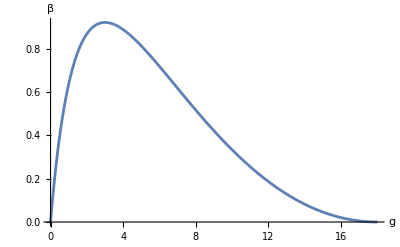

```mathematica
(* solve condition for β to obtain a function β(g) *)
(* NOTE: curve is the only solution in a relevant parameter regime, but is only valid for 0 <= g <= 18, at g=18, the curve vanishes and becomes invalid *)
curve=FullSimplify[Solve[2 k^2 (-18+g+k^2)+3 (12+g+k^2) β==0/.k->kmc,β]][[3]]
(* calculate roots of curve *)
Solve[(β/.curve)==0,g]
(* plot parameter curve on which N=0 for 0 < g < 18 *)
Plot[β/.curve,{g,0,18},AxesLabel->{g,β}]
```

### Plots of parameters on {N=0}

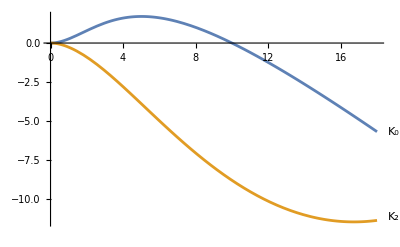

```mathematica
(* plot coefficients on the parameter line N(β,g)=0*)
Plot[{Labeled[K0/.curve,"K_0"],Labeled[K2/.curve,"K_2"]},{g,0,18}]
```

```mathematica
(* check that miracle is actually true and K_0(β(g),g)=0 at g=10 *)
(K0/.β->(216+87 g+2 g^2-√(46656+34992 g+7425 g^2+484 g^3))/(3 (2+g)))/.g->10
```

{0}

```mathematica
(* Write coefficients on {N=0} to file *)
Export[FileNameJoin[{NotebookDirectory[],"K0-coeffs-on-Nzero.txt"}],{K0/.curve}];
Export[FileNameJoin[{NotebookDirectory[],"K2-coeffs-on-Nzero.txt"}],{K2/.curve}];
```

## Coefficients on square lattice

Remark: Since the self-interaction term is the same as for the hexagonal lattice, we only calculate the cross-interaction coefficient.

```mathematica
(* wavevectors for square lattice *)
k1Square=k*{1,0}
k2Square=k*{0,1}
```

{k,0}

{0,k}

```mathematica
(* relevant non-central terms *)
ν2k=FullSimplify[-Inverse[Lhat[k1Square[[1]]+k1Square[[1]],k1Square[[2]]+k1Square[[2]]]].N2[Exp[I*k1Square.{x1,x2}],Exp[I*k1Square.{x1,x2}],Exp[I*k1Square.{x1,x2}]*α,Exp[I*k1Square.{x1,x2}]*α]*Exp[-2*I*k1Square.{x1,x2}]]
νjmlSquare=FullSimplify[-2*Inverse[Lhat[k1Square[[1]]-k2Square[[1]],k1Square[[2]]-k2[[2]]]].N2[Exp[I*k1Square.{x1,x2}],Exp[-I*k2.{x1,x2}],Exp[I*k1Square.{x1,x2}]*α,Exp[-I*k2.{x1,x2}]*α]*Exp[-I*(k1Square-k2).{x1,x2}]]
νjplSquare=FullSimplify[-2*Inverse[Lhat[k1Square[[1]]+k2Square[[1]],k1Square[[2]]+k2[[2]]]].N2[Exp[I*k1Square.{x1,x2}],Exp[I*k2Square.{x1,x2}],Exp[I*k1Square.{x1,x2}]*α,Exp[I*k2Square.{x1,x2}]*α]*Exp[-I*(k1Square+k2Square).{x1,x2}]]
```

{{(k^2 (48 (g+k^2)-(27+2 g+2 k^2) M)+6 (g+k^2) β)/(k^2 (g (-48+M)+4 k^2 (-48+M)+72 M)-12 (g+4 k^2) β)},{(k^2 (-16 (g+k^2) (g+4 k^2)+(g (42+g)+(96+5 g) k^2+4 k^4) M-(27+2 g+2 k^2) M^2)+6 (g+k^2) M β)/(k^2 M (g (-48+M)+4 k^2 (-48+M)+72 M)-12 (g+4 k^2) M β)}}

{{(192 (7 k^2 (24 (g+k^2)-(15+g+k^2) M)+48 (g+k^2) β))/(49 k^2 (4 g (-48+M)+7 k^2 (-48+M)+288 M)-1344 (4 g+7 k^2) β)},{(168 k^2 (-16 (g+k^2) (4 g+7 k^2)+(4 g (44+g)+(236+11 g) k^2+7 k^4) M-8 (15+g+k^2) M^2)+9216 (g+k^2) M β)/(7 M (7 k^2 (4 g (-48+M)+7 k^2 (-48+M)+288 M)-192 (4 g+7 k^2) β))}}

{{(896 k^2 (24 (g+k^2)-(18+g+k^2) M)+6144 (g+k^2) β)/(49 k^2 (4 g (-48+M)+7 k^2 (-48+M)+288 M)-1344 (4 g+7 k^2) β)},{(112 k^2 (-16 (g+k^2) (4 g+7 k^2)+(4 g (48+g)+11 (24+g) k^2+7 k^4) M-8 (18+g+k^2) M^2)+6144 (g+k^2) M β)/(7 M (7 k^2 (4 g (-48+M)+7 k^2 (-48+M)+288 M)-192 (4 g+7 k^2) β))}}

```mathematica
(* calculate cross coefficients from quadratic interactions *)
Γ0Square=Γ0
Γ3pSquare=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[-I*k2Square.{x1,x2}],Exp[I*(k1Square+k2Square).{x1,x2}]*η1,Exp[-I*k2Square.{x1,x2}]*α,Exp[I*(k1Square+k2Square).{x1,x2}]*η2]*Exp[-I*k1Square.{x1,x2}]/.{η1->νjplSquare[[1]][[1]],η2->νjplSquare[[2]][[1]]}]]
Γ3mSquare=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N2[Exp[I*k2Square.{x1,x2}],Exp[I*(k1Square-k2Square).{x1,x2}]*η1,Exp[I*k2Square.{x1,x2}]*α,Exp[I*(k1Square-k2Square).{x1,x2}]*η2]*Exp[-I*k1Square.{x1,x2}]/.{η1->νjmlSquare[[1]][[1]],η2->νjmlSquare[[2]][[1]]}]]
```

{0}

{(14 k^6 (-96 (g+k^2) (4 g (15+g)+(123+13 g) k^2+9 k^4)+2 (4 g (1512+g (147+g))+(7992+g (1581+19 g)) k^2+(993+26 g) k^4+11 k^6) M-3 (1728+4 g (60+g)+13 (24+g) k^2+9 k^4) M^2)-24 k^4 (16 (g+k^2) (8 g (30+g)+3 (167+8 g) k^2+16 k^4)-3 (12 g (116+5 g)+(1896+187 g) k^2+127 k^4) M) β-27648 k^2 (g+k^2) (g+2 k^2) β^2)/(21 (k^4+k^2 (3+g-M)+3 β) (7 k^2 (4 g (-48+M)+7 k^2 (-48+M)+288 M)-192 (4 g+7 k^2) β))}

{(7 k^6 (-96 (g+k^2) (4 g (15+g)+(123+13 g) k^2+9 k^4)+2 (4 g (1440+g (147+g))+(7380+g (1569+19 g)) k^2+(981+26 g) k^4+11 k^6) M-3 (1440+4 g (58+g)+(292+13 g) k^2+9 k^4) M^2)-12 k^4 (16 (g+k^2) (8 g (30+g)+3 (167+8 g) k^2+16 k^4)-3 (4 g (334+15 g)+(1756+187 g) k^2+127 k^4) M) β-13824 k^2 (g+k^2) (g+2 k^2) β^2)/(7 (k^4+k^2 (3+g-M)+3 β) (7 k^2 (4 g (-48+M)+7 k^2 (-48+M)+288 M)-192 (4 g+7 k^2) β))}

```mathematica
(* calculate cross coefficients from cubic interactions *)
Λ2Square=FullSimplify[Expand[(1/(α+alphaTilde))*{alphaTilde,1}.N3[Exp[I*k1Square.{x1,x2}],Exp[I*k2Square.{x1,x2}],Exp[-I*k2Square.{x1,x2}],Exp[I*k1Square.{x1,x2}]*α,Exp[I*k2Square.{x1,x2}]*α,Exp[-I*k2Square.{x1,x2}]*α]*Exp[-I*k1Square.{x1,x2}]]]
```

{-(k^2 (g+k^2) (k^2 (8 (6+g+k^2)-7 M)+48 β))/(72 (k^4+k^2 (3+g-M)+3 β))}

```mathematica
(* cross interaction coefficient *)
K1Square=Simplify[Expand[((2*Γ0Square+2*Γ3pSquare+2*Γ3mSquare+6*Λ2Square)/.M->Mmc[k])/.k->kmc]]
```

{(16 g (72+g-β) β (8584704 √2 (-72+β)^6 β^2 √(g (72+g-β) β)+280 g^7 β (1934917632+1209323520 β+78382080 β^2+1088640 β^3+3240 β^4+β^5)-2 g^6 (1170348 β^6+407 β^7-290304 β^4 (15039+25 √2 √(g (72+g-β) β))-240 β^5 (-1126098+35 √2 √(g (72+g-β) β))-22394880 β^3 (58956+49 √2 √(g (72+g-β) β))-1289945088 β (-20682+175 √2 √(g (72+g-β) β))-107495424 β^2 (146889+350 √2 √(g (72+g-β) β)))+31104 g (-72+β)^5 β (120 β^3+190944 √2 √(g (72+g-β) β)-36 β (-6768+451 √2 √(g (72+g-β) β))+β^2 (-12024+485 √2 √(g (72+g-β) β)))-6 g^5 (-72+β) (-295697 β^6-89 β^7-180592312320 √2 √(g (72+g-β) β)+26873856 β (-903672+167 √2 √(g (72+g-β) β))+13436928 β^2 (-53994+1087 √2 √(g (72+g-β) β))+134784 β^3 (2114856+4501 √2 √(g (72+g-β) β))+864 β^4 (2939076+5599 √2 √(g (72+g-β) β))+β^5 (-65656152+6383 √2 √(g (72+g-β) β)))+216 g^2 (-72+β)^4 β (43648 β^4-25920 β (-115344+173 √2 √(g (72+g-β) β))+373248 (-50256+227 √2 √(g (72+g-β) β))-3 β^3 (686256+1669 √2 √(g (72+g-β) β))-24 β^2 (4831056+27745 √2 √(g (72+g-β) β)))+108 g^3 (-72+β)^3 (-1012 β^6-5518098432 √2 √(g (72+g-β) β)+β^5 (-277972+19 √2 √(g (72+g-β) β))+2 β^4 (2808288+1849 √2 √(g (72+g-β) β))+746496 β (-117360+2479 √2 √(g (72+g-β) β))+48 β^3 (23620032+15155 √2 √(g (72+g-β) β))+3456 β^2 (6197472+43909 √2 √(g (72+g-β) β)))+3 g^4 (-72+β)^2 (-76086 β^6-162533081088 √2 √(g (72+g-β) β)+1990656 β^2 (-2568861+304 √2 √(g (72+g-β) β))+β^5 (-23199408+5501 √2 √(g (72+g-β) β))-8957952 β (1482192+21533 √2 √(g (72+g-β) β))+24192 β^3 (2900880+21977 √2 √(g (72+g-β) β))+96 β^4 (22001112+52033 √2 √(g (72+g-β) β)))))/(63 (-72+β)^4 (864+12 g-12 β+√2 √(g (72+g-β) β)) (g β+6 √2 √(g (72+g-β) β))^2 (12 β^4-1728 √2 (216+27 g+g^2) √(g (72+g-β) β)+β^3 (-2592+60 g+4 g^2+15 √2 √(g (72+g-β) β))+β^2 (-8640 g+504 g^2-4 g^3+33 √2 g √(g (72+g-β) β)+72 (2592-31 √2 √(g (72+g-β) β)))-72 β (12 g^3+72 (864-17 √2 √(g (72+g-β) β))+24 g (-180+√2 √(g (72+g-β) β))+g^2 (792+√2 √(g (72+g-β) β)))))}

```mathematica
(* Write expression for Subscript[K, 1] to file *)
Export[FileNameJoin[{NotebookDirectory[],"cross-cubic-coeffs-square.txt"}],{K1Square/.β->b}];
```

## Plot coefficients on the square lattice

Here, we plot the coefficients K_0 and K_1 in the (β,g)-parameter plane. We then plot the regions of parameter space, where certain existence and selection criteria for roll waves and square patterns are satisfied.

### Density plots of coefficients K_0 and K_1

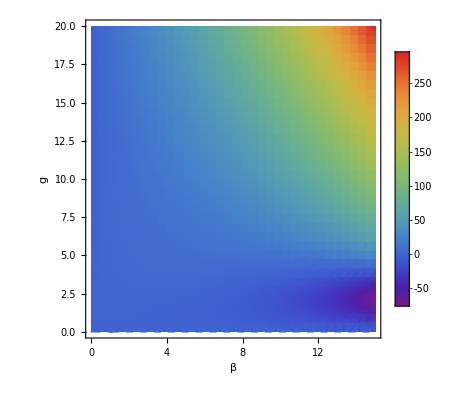

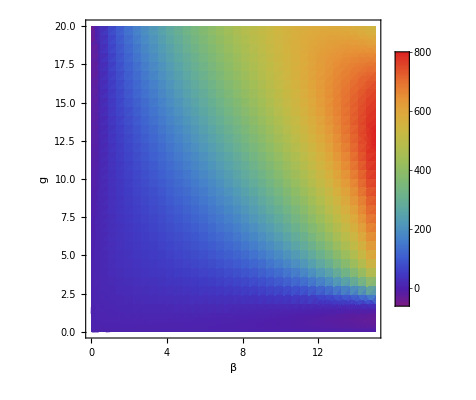

```mathematica
(* Density plot of self-interaction coefficient Subscript[K, 0] *)
DensityPlot[K0,{β,0.001,15},{g,0,20},ColorFunction->"Rainbow",PlotPoints->35,PlotLegends->Automatic,MeshFunctions->{#3 &},Mesh->{{0}},MeshStyle->{White,Dashed},FrameLabel->{β,g}]
(* Density plot of self-interaction coefficient Subscript[K, 1] *)
DensityPlot[K1Square,{β,0.001,15},{g,0,20},ColorFunction->"Rainbow",PlotPoints->35,PlotLegends->Automatic,MeshFunctions->{#3 &},Mesh->{{0}},MeshStyle->{White,Dashed},FrameLabel->{β,g}]
```